```mathematica
ClearAll[files, importfile, raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/322(4.8)/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/322(4.8)/f1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/322(4.8)/~$Книга1.xlsx}

```mathematica
importfile = files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/322(4.8)/Книга1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

```mathematica
dataset1=makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"x"->(Around[#x,#dx]&),"L"->(Around[#L,#dL]&)|>]
```

Dataset[<>]

```mathematica
dataset2=makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"x"->(Around[#x,#dx]&),"L"->(Around[#r,#dr]&)|>]
```

Dataset[<>]

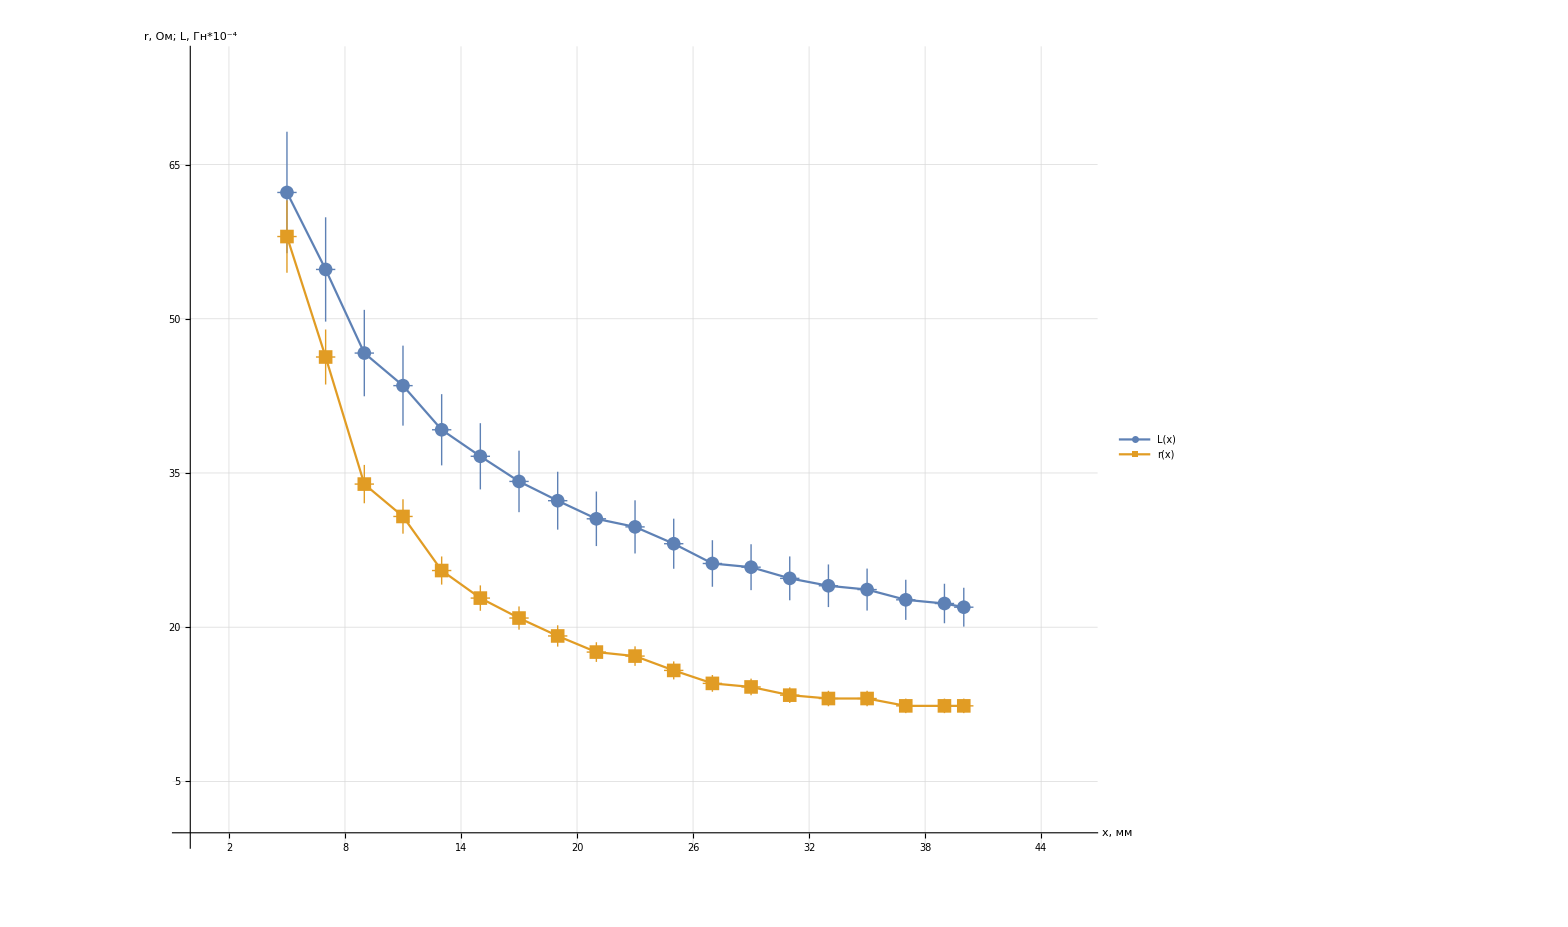

```mathematica
Show[
ListPlot[
{dataset1WithErrs,dataset2WithErrs},
Joined->True,
AxesLabel->{Style["x, мм",Large],Style["r, Ом; L, Гн*10^-4",Large]},
AxesStyle->Directive[Arrowheads[{0.02}],Black], 
ImageSize->1500,
GridLines->{Range[-10,430,1], Range[-10,500,2]},
Ticks-> {Range[-10,420,2],Range[-10,500,5]}, 
TicksStyle->20,
PlotRange->{{0,46},{0,75}},
PlotMarkers->{Automatic,14},
PlotLegends->Placed[LineLegend[
Automatic,
{"L(x)", " r(x)"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.6],Scaled[0.6]}
]
]
]
```

```mathematica
UR = 69;
UL = 80;
Url = 107;
```

```mathematica
eq = Normal[{α,ϕ}/.Solve[Url*Cos[α]==UR+UL*Cos[ϕ] && Url* Sin[α] == UL*Sin[ϕ],{α,ϕ}]]
```

{{-ArcTan[(64 √826)/1635]+2 π C[1],-ArcTan[(4 √826)/3]+2 π C[2]},{ArcTan[(64 √826)/1635]+2 π C[1],ArcTan[(4 √826)/3]+2 π C[2]}}

```mathematica
mya = eq⟦2,1⟧ - 2π C[1]
```

ArcTan[(√75047)/173]

```mathematica
myf = eq⟦2,2⟧ - 2π C[2]
```

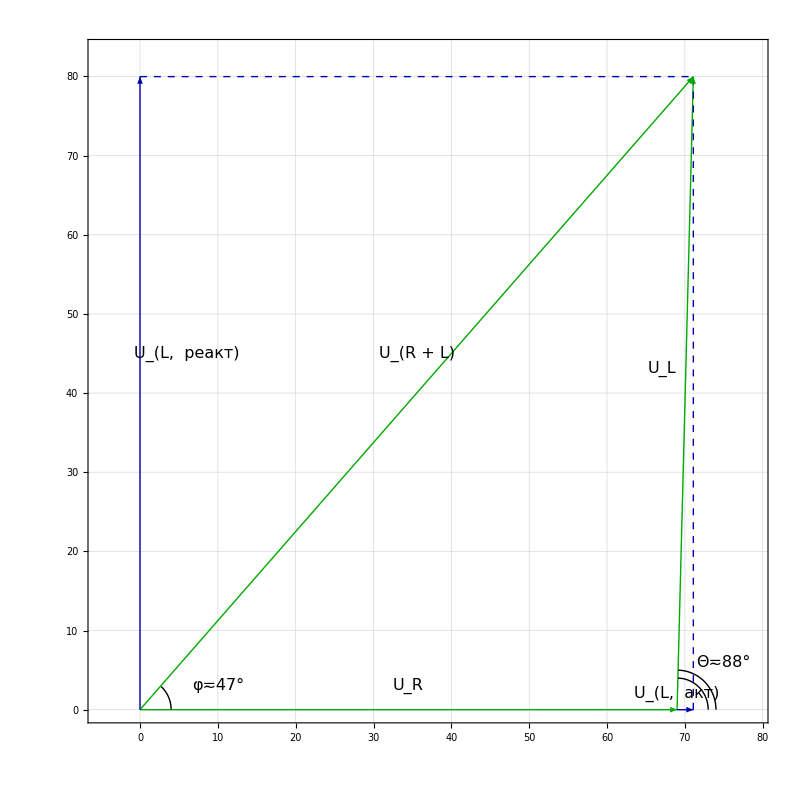

```mathematica
Graphics[
{
{Darker@Green,
{Arrowheads[0.03],Thick,Arrow[{{0,0}, {UR,0}}]}, 
{Arrowheads[0.03],Thick,Arrow[{{0,0},{Url*Cos[ArcTan[(64*√826)/1635]],Url*Sin[ArcTan[(64*√826)/1635]]}}]},
{Arrowheads[0.03],Thick,Arrow[{{UR,0},{Url*Cos[ArcTan[(64*√826)/1635]],Url*Sin[ArcTan[(64*√826)/1635]]}}]}},
Circle[{0,0}, 4, {0,ArcTan[(480 √133)/5203]}],
Circle[{UR,0}, 4, {0,ArcTan[(80 √133)/27]}],
Circle[{UR,0}, 5, {0,ArcTan[(80 √133)/27]}],
{Darker@Blue,
{Dashed,
Line[{{0,Url*Sin[ArcTan[(64*√826)/1635]]},{Url*Cos[ArcTan[(64*√826)/1635]],Url*Sin[ArcTan[(64*√826)/1635]]}}],
Line[{{Url*Cos[ArcTan[(64*√826)/1635]],0},{Url*Cos[ArcTan[(64*√826)/1635]],Url*Sin[ArcTan[(64*√826)/1635]]}}]
},
{Arrowheads[0.03],Thick,Arrow[{{0,0}, {0,Url*Sin[ArcTan[(64*√826)/1635]]}}]},
{Arrowheads[0.015],Thick,Arrow[{{UR,0}, {Url*Cos[ArcTan[(64*√826)/1635]],0}}]}
}
},
PlotRange->{{-5,UR+10},{0,83}},
ImageSize->800,
GridLines->{Range[-10,430,2.5], Range[-8,500,2.5]},
Frame -> True,
Epilog->{
Inset[
Style["U_R", 16], {UR/2,3}
],
Inset[
Style["U_(R + L)", 16], {Url*Cos[ArcTan[(64*√826)/1635]]/2, Url*Sin[ArcTan[(64*√826)/1635]]/2+5}
],
Inset[
Style["φ≂47°",16], {10,3}
],
Inset[
Style["Θ≂88°",16], {UR+6,6}
],
Inset[
Style["U_(L,  :0440:0435:0430:043a:0442)",16], {6,90/2}
],
Inset[
Style["U_(L,  :0430:043a:0442)",16], {UR,2}
],
Inset[
Style["U_L",16], {UR-2,43}
]
}
]
```

```mathematica
Url*Sin[ArcTan[(64*√826)/1635]]
```

(64 √826)/23

```mathematica
ArcTan[(480 √133)/5203]
```

ArcTan[(480 √133)/5203]

```mathematica
Cos[ArcTan[(4 √826)/3]]
```

3/115

```mathematica
AngleVector
Circle
```

```mathematica
φ
```

```mathematica
CalloutMarker
```

```mathematica
Labeled[Arrow[{{0,0}, {69,0}}],"U_R"]
```

Arrow[{{0,0},{69,0}}]U_R

```mathematica
"U_R", Spacings->{Automatic,0},
```

```mathematica
GridLines->{Range[-10,430,1], Range[-10,500,2]}
```

```mathematica
80, 107
```

```mathematica
Manipulate[
Graphics[
{Thickness[0.01],
(* Vt - Green *)
RGBColor[0,0.46,0.05],
Arrow[{{0,0},{Vt,0}}],

(* It - Orange *)
RGBColor[1,.47,0],
Arrow[{{0,0},{It,It*Tan[(θ/(180/π))]}}],

(* (Ra * It) - Blue *)
ColorData["HTML","SlateBlue"]
,Arrow[{{Vt,0},{(Vt+(It*Ra)),(It*Ra*Tan[(θ/(180/π))])}}],

(* ((Xa + Xs) * It) - Brown *)
Brown,Arrow[{{(Vt+(It*Ra)),(It*Ra*Tan[(θ/(180/π))])},{(Vt+(It*Ra)+(It*Xs*Cos[(θ/(180/π))+π/2])),((It*Ra*Tan[(θ/(180/π))])+(It*Xs*Sin[(θ/(180/π))+π/2]))}}],

(* (((Xa + Xs) + Ra) * It) - Black *)
Black,Arrow[{{Vt,0},{eg1=(Vt+(It*Ra)+(It*Xs*Cos[(θ/(180/π))+π/2])),eg2=((It*Ra*Tan[(θ/(180/π))])+(It*Xs*Sin[(θ/(180/π))+π/2]))}}],

(* generated voltage (Eg) - Violet *)
RGBColor[1,0,.47],Arrow[{{0,0},{eg1,eg2}}]},

Axes->True,
FrameLabel->{"real","reactive"},
LabelStyle->Directive[Black,Bold],
PlotLabel->"Synchronous Machine",
PlotRange->{{0,850},{-500,500}},
PlotRangeClipping->True,
Frame->True,
ImageSize->{400, 400},

(* add text box insets as epilog *)
Epilog->{
Inset[Framed[Style[
"E_g",10,RGBColor[1,0,.47],Bold],
Background->LightYellow],{(eg1/1.25),(eg2/1.25)}],

Inset[Framed[Style[
If[θ>-1 && θ< 1 ,"power factor = unity",
If[θ>0,"power factor = leading","power factor = lagging"]]
,14],Background->LightYellow],{550,-420}],

Inset[Framed[Style[Row[{
"power angle = ", NumberForm[SetPrecision[Chop[(ArcTan[eg2/eg1]*180/π)],2],{2,2}]}],14],Background->LightYellow],{550,-320}]
}
(* end of epilog for vector plot *)
],
(* add sliders *) 
Style["bus parameters", Bold],
Style["terminal voltage (Vt)",
RGBColor[0,0.46,0.05], Bold],
{{Vt,480,""},
400,600,.01,Appearance->"Labeled",ImageSize->Small},
Style["line current (I_t)",
RGBColor[1,.47,0], Bold],
{{It,100,""},
0,200,.01,Appearance->"Labeled",ImageSize->Small},
"phase angle (pf)",
{{θ ,-15,""},
-80,80,.01,Appearance->"Labeled",ImageSize->Small},
Delimiter,
Style["machine parameters", Bold],
Style["armature resistance (R_a)",
ColorData["HTML","SlateBlue"],Bold],
{{Ra,0.5,"R_a"},
0.1,0.75,.01,Appearance->"Labeled",ImageSize->Small},
Style["reactances (X_s + X_a)",Brown,Bold],
{{Xs,1.0,"X_s"},
0.2,1.50,.01,Appearance->"Labeled",ImageSize->Small},
ControlPlacement->Left,TrackedSymbols:>Manipulate
]
```

Доказать равенства:

```mathematica
sin^2 x = (1-cos(2x))/2
```

```mathematica
sin(2x) = 2sin(x)cos(x)
```

```mathematica
tg^2 x = 1/(cos^2 x)-1
```

```mathematica
cos(2x) = (1-tg^2 x)/(1+ tg^2 x)
```

```mathematica
sin (2 x) = (2 tg x)/(1+tg^2 x)
```

Разобраться с формулами приведения. Что будет если заменить α на -α ?

```mathematica
cos(α+π/2) = ?
```

```mathematica
cos(α+π) = ?
```

```mathematica
cos(α+(3π)/2) = ?
```

```mathematica
cos(α+2π) = ?
```

```mathematica
sin(α+π/2) = ?
```

```mathematica
sin(α+π) = ?
```

```mathematica
sin(α+(3π)/2) = ?
```

```mathematica
sin(α+2π) = ?
```

Выразить через sinα или cosα:

```mathematica
sin(3α)=?
```

```mathematica
cos(4α) =?
```